## Walker — PS 5 — 2025-02-04

## EIWL3 Sections 14 and 17

## Section 14

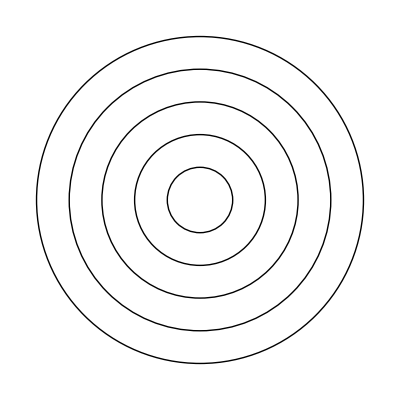

```mathematica
Graphics[Table[Circle[{0,0},r],{r,5}]]
```

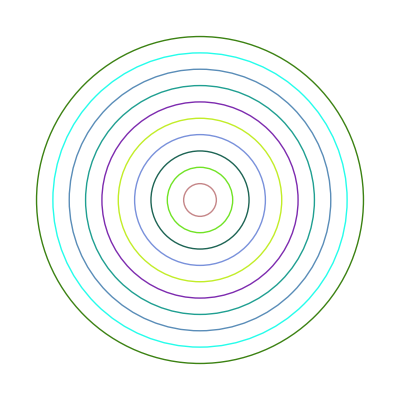

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,10}]]
```

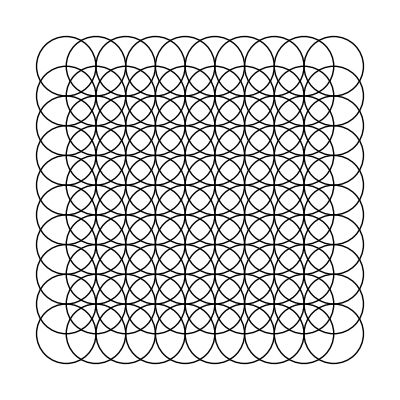

```mathematica
Graphics[Table[Circle[{x,y},1],{x,10},{y,10}]]
```

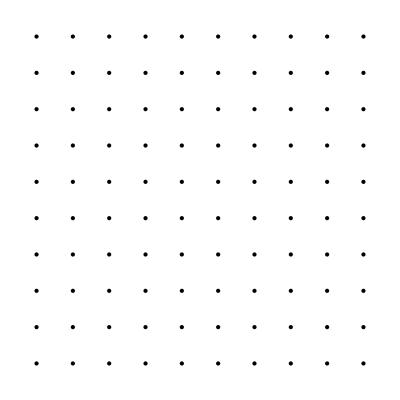

```mathematica
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,m}]],{m,1,20,1}]
```

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},0.5],RGBColor[{x/10,y/10,z/10}]],{x,0,10,1},{y,0,10,1},{z,0,10,1}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,10}]],{t,-2,2}]
```

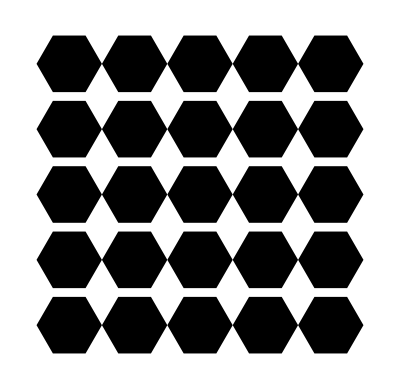

```mathematica
Graphics[Table[RegularPolygon[{x,y},0.5,6],{x,1,5,1},{y,1,5,1}]]
```

```mathematica
Graphics3D[Line[Table[RandomInteger[50,3],50]]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Style[Icosahedron[p],Opacity[0.5]],Style[Dodecahedron[1],Opacity[0.5]]}],{p,1,2}]
```

## Section17

```mathematica
UnitConvert[,]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],]
```

96.963 km/h

```mathematica
UnitConvert[["Height"],]
```

0.205052 mi

```mathematica
Entity["Mountain","MountEverest"]["Elevation"]/["Height"]
```

26.8147

```mathematica
["Mass"]/["Mass"]
```

81.3

```mathematica
UnitConvert[,]
```

16.44 $

```mathematica
UnitConvert[{,,},]
```

{317514659/320000000 kg,226.796 kg,408233133/20000000 kg}

```mathematica
UnitConvert[EntityValue[EntityList["Planet"],"DistanceFromEarth"],]
```

{11.4194 light minutes,3.66378 light minutes,0. light minutes,6.19703 light minutes,39.2374 light minutes,87.3814 light minutes,162.485 light minutes,255.37 light minutes}

```mathematica
Rotate["hello",180Degree]
```

hello

```mathematica
Table[Rotate[Style["A",100],r Degree],{r,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate[["Image"],r Degree],{r,0,180}]
```

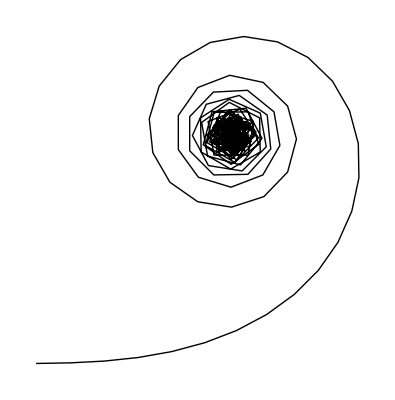

```mathematica
Graphics[Line[AnglePath[Range[180]Degree]]]
```

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[n Degree,100]]]],{n,0,360}]
```

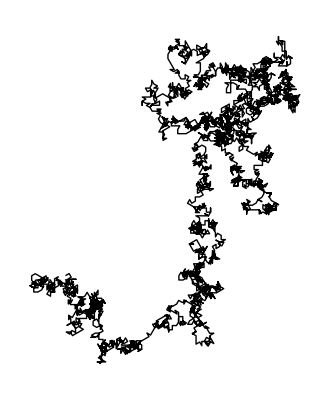

```mathematica
Graphics[Line[AnglePath[IntegerDigits[2^10000]*30 Degree]]]
```